## Define Mueller Matrices

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
(*General Retarder*)
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2 Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
(* Retarder at 0 degrees *)
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
(* Linear Polarizer at 0 with  k value *)
LPzeroWithK[δ_,k1_]:=1/2({{1, k1, 0, 0}, {k1, 1, 0, 0}, {0, 0, √(1-k1^2), 0}, {0, 0, 0, √(1-k1^2)}});
(* Perfect linear polarizer *)
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
(* We can rotate optical elements and input polarization with the following matrix *)
	MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}})
(* An optical element at an arbitrary angle can be obtained by rotating the matrix. Since it's a matrix we're rotating and not a vector,
	we must multiply by the matrix and the transpose, like so *)
LP[θ_]:=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]]
```

## Play Around with them

## We will assume our incident vector was 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {1}, {0}, {0}});
```

## First, we pass the light through a horizontal linear polarizer and a vertical linear polarizer.

### First Horizontal

```mathematica
LPzero.inc
```

{{1},{1},{0},{0}}

The stokes vector is unaffected, as we would expect.

### Then vertical

```mathematica
vertLP=MuellerRotation[π/2].LPzero.Transpose[MuellerRotation[π/2]];
MatrixForm[vertLP.inc]
```

(0
0
0
0)

The stokes vector is completely extinguished, as we would expect.

### Now we want to have an arbitrary linearly polarized input, and see how the intensity changes as the angle changes for both the vertical polarizer and the horizontal polarizer. We begin the arbitrary polarization at 45°.

```mathematica
(* We start with a horizontally polarized stokes vector. *)
inc=({{1}, {1}, {0}, {0}});
(* We can define the linear polarizer at an arbitrary angle by rotating the LP that is at zero.*)
arbLP[θ_]:=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]];

(* We can define an arbitrary linearly polarized stokes vector by rotating the stokes vector itself. *)
arbinc=MuellerRotation[θ].inc;

(* Here we can see the equation the governs the arbitrary input *)
MatrixForm[arbinc]

(* Here we evaluate the arbitrary input to a specific angle using a replacement rule *)
MatrixForm[arbinc/.θ->π/4]
```

(1
Cos[2 θ]
Sin[2 θ]
0)

(1
0
1
0)

## Simulating Polarimeter Data

```mathematica
tickM=Range[0,2π,π/2];
```

{0,π/2,π,(3 π)/2,2 π}

```mathematica
(* Import the package to analyze the simulated data. *)
SetDirectory[$PACKAGES]
Import["polarization.wl"]
```

C:\Users\karla\Box Sync\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\packages

92

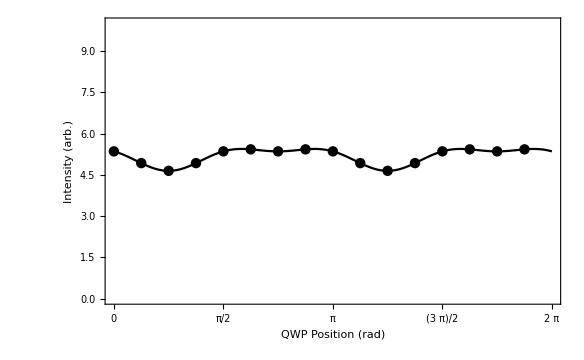

```mathematica
p0=10;
p1=1/Sqrt[2]/10;
p2=0;
p3=1/Sqrt[2]/10;

alpha=0;

beta=68.7*π/180*0;
beta=0;
counts=1000;
noiseMultiplier=0;
currentNoise=0;
retard=.25*2*π;

inc=({{p0}, {p1}, {p2}, {p3}}); (* Stokes vector to simulate *)

inc=UnNormalizeStokes[inc];
pl=Plot[{(LP[alpha*π/180].MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]},{θ,0,2π},AxesOrigin->{0,0},ImageSize->{720,450},PlotStyle->colorBlindPalette[[1]],PlotRange->{0,10}];

PolarimeterDataGenerator[angle_]:=(LP[alpha].MuellerRotation[angle].LRzero[retard].Transpose[MuellerRotation[angle]].inc)[[1]][[1]];
angles=Range[0,2π,2π/16];
angles=angles[[;;-2]];
SeedRandom[]
seeder=RandomInteger[{0,99}];
seeder=92
seeds=Range[0,Length[angles]];
polData={};
For[i=1,i≤Length[angles],i++,
SeedRandom[seeder+seeds[[i]]];
noise=(currentNoise+Sqrt[counts]/counts*noiseMultiplier)*p0*RandomReal[{-1/2,1/2}];
AppendTo[polData,PolarimeterDataGenerator[angles[[i]]]+noise];
]
plotData=Transpose[{angles,polData}];

p=Show[{ListPlot[{plotData},PlotRange->{0,10},PlotStyle->colorBlindPalette],pl},FrameLabel->{"QWP Position (rad)","Intensity (arb.)"},PlotRange->{0,10},polarimeterPlotOptions,PlotRange->{0,10}]
```

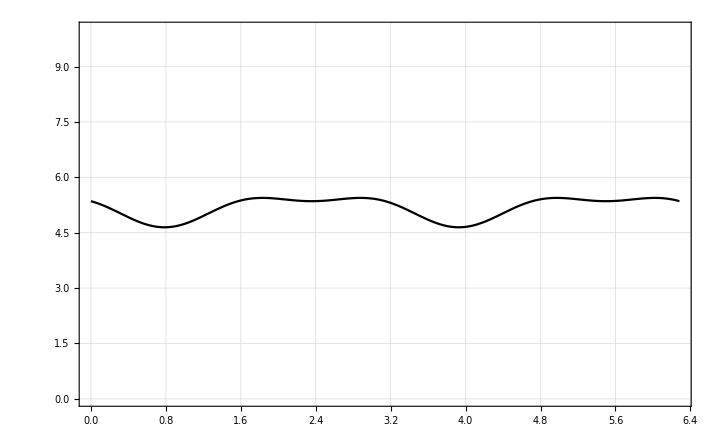

```mathematica
pl
```

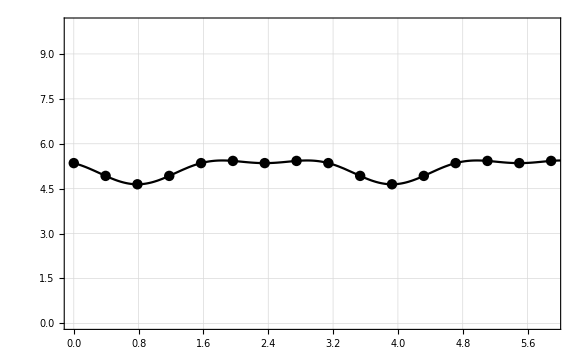

```mathematica
Show[{ListPlot[{plotData},PlotRange->{0,10},PlotStyle->colorBlindPalette],pl}]
```

<|Sin Coefficients→<|0→0.,1→-5.55112×10^-17,2→-3.53553,3→0.,4→0.,5→0.,6→2.22045×10^-16,7→2.77556×10^-17|>,Cos Coefficients→<|0→6.76777,1→-4.44089×10^-16,2→0.,3→5.55112×10^-17,4→1.76777,5→-5.55112×10^-17,6→0.,7→0.|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>

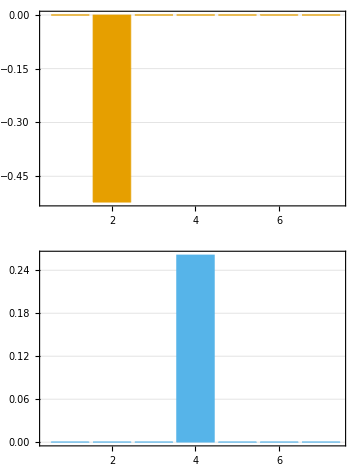

```mathematica
fc=DFT[polData]
fcg=FourierCoefficientBarChart[fc];
fcgg=GraphicsGrid[{{fcg[[1]]},{fcg[[2]]}},ImageSize->Medium]
```

```mathematica
s=fc["Sin Coefficients"];
c=fc["Cos Coefficients"];
beta=0;
stokes=CalculateStokesFromFourierCoefficients[c[0],c[2],c[4],s[2],s[4],1,0,0,π/2]
stokesV=MatrixForm[Transpose[{Chop[stokes//Values,10^-5]}]]
```

<|p0→5.,p1→0.707107,p2→0.,p3→0.707107|>

(5.
0.707107
0
0.707107)

{1/2+1/2 Cos[2 θ]^2-(0.-3.06162×10^-17 Sin[2 θ]) Sin[2 θ]}

RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]]

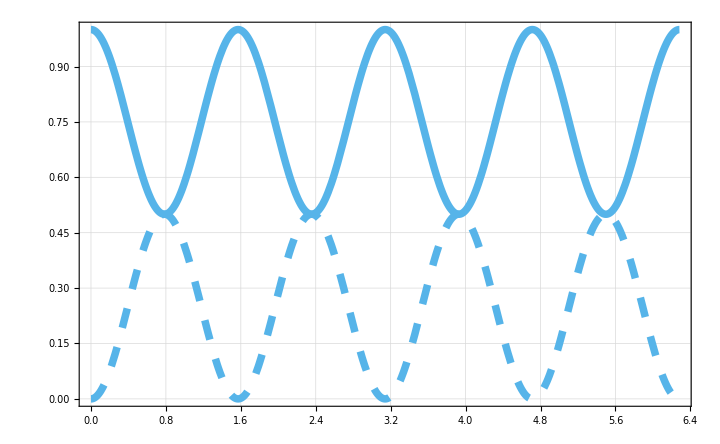

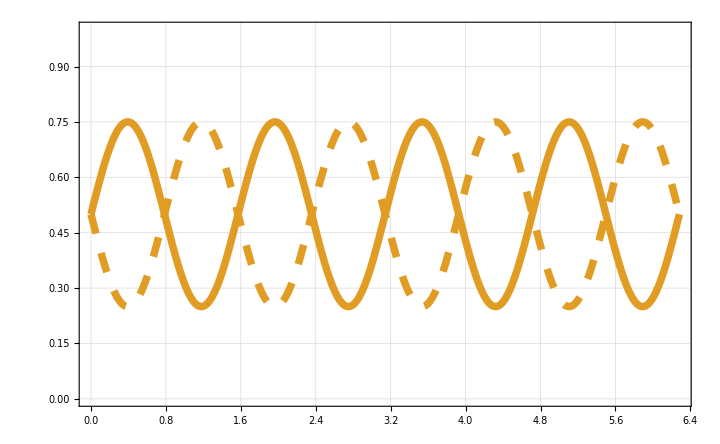

{0.5-0.5 Sin[2 θ]}

{0.5+0.5 Sin[2 θ]}

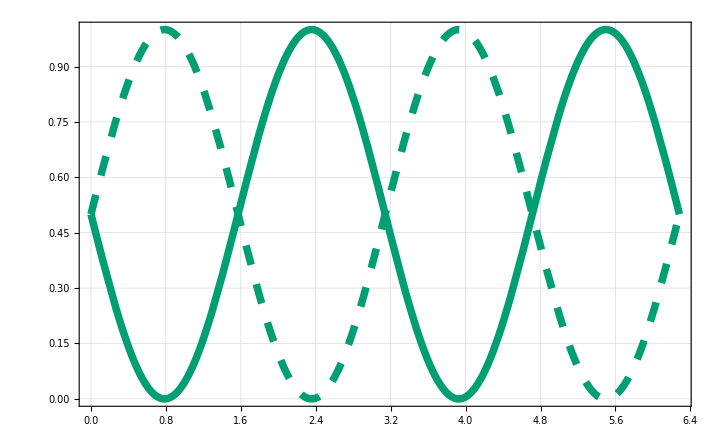

```mathematica
inc=({{1}, {1}, {0}, {0}});

retard=.25*2*π;
horizontal=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]

inc=({{1}, {-1}, {0}, {0}});
blue=colorBlindPalette[[3]]
color=blue;
thickness=.0075;
dashThick1=.02;
dashThick2=.02;
vertical=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
Plot[{horizontal,vertical},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]

inc=({{1}, {0}, {1}, {0}});
plus45=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
inc=({{1}, {0}, {-1}, {0}});
orange=ColorData[97,"ColorList"][[2]];
color=orange;
minus45=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]];
Plot[{plus45,minus45},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]
inc=({{1}, {0}, {0}, {1}});
rcp=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]
inc=({{1}, {0}, {0}, {-1}});
green=colorBlindPalette[[4]];
color=green;
lcp=(LPzero.MuellerRotation[θ].LRzero[retard].Transpose[MuellerRotation[θ]].inc)[[1]]
Plot[{rcp,lcp},{θ,0,2π},PlotStyle->{{color,Thickness[thickness]},{color,Dashing[{dashThick1,dashThick2}],Thickness[thickness]}},AxesOrigin->{0,0},ImageSize->{720,450},PlotRange->{0,1}]
```

## Keith

```mathematica
result=LPzero.LRzero[r1].LR[θ,r2].LPzero.({{Io}, {Mo}, {Co}, {So}})
```

{{Co k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-k1 √(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))+Io (1+k1^2 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{Co √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-√(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1^2+Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2)+Io (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{√(1-k1^2) So (√(1-k1^2) Cos[2 π r2] Sin[r1]+√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2])+Io k1 (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Mo (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2]+√(1-k1^2) Cos[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2))},{√(1-k1^2) So (√(1-k1^2) Cos[r1] Cos[2 π r2]-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2])+Io k1 (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Mo (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2]-√(1-k1^2) Sin[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2))}}

```mathematica
MatrixForm[result]
```

(Co k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-k1 √(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))+Io (1+k1^2 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))
Co √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-√(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1^2+Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2)+Io (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))
√(1-k1^2) So (√(1-k1^2) Cos[2 π r2] Sin[r1]+√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2])+Io k1 (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Mo (√(1-k1^2) Cos[r1] (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Sin[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2]+√(1-k1^2) Cos[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2))
√(1-k1^2) So (√(1-k1^2) Cos[r1] Cos[2 π r2]-√(1-k1^2) Cos[2 θ] Sin[r1] Sin[2 π r2])+Io k1 (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Mo (-√(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[r1] Sin[2 θ]+√(1-k1^2) Cos[r1] Sin[2 π r2] Sin[2 θ])+Co √(1-k1^2) (-√(1-k1^2) Cos[r1] Cos[2 θ] Sin[2 π r2]-√(1-k1^2) Sin[r1] (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2)))

```mathematica
result=LPzero.LR[θ,r2].LPzero.({{Io}, {Mo}, {Co}, {So}})
```

{{Co k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-k1 √(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))+Io (1+k1^2 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{Co √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]-√(1-k1^2) So Sin[2 π r2] Sin[2 θ]+Mo (k1^2+Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2)+Io (k1+k1 (Cos[2 θ]^2+Cos[2 π r2] Sin[2 θ]^2))},{(1-k1^2) So Cos[2 θ] Sin[2 π r2]+Io k1 √(1-k1^2) (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+√(1-k1^2) Mo (1-Cos[2 π r2]) Cos[2 θ] Sin[2 θ]+Co (1-k1^2) (Cos[2 π r2]^2 Cos[2 θ]+Sin[2 θ]^2)},{(1-k1^2) So Cos[2 π r2]-Co (1-k1^2) Cos[2 θ] Sin[2 π r2]+Io k1 √(1-k1^2) Sin[2 π r2] Sin[2 θ]+√(1-k1^2) Mo Sin[2 π r2] Sin[2 θ]}}